```mathematica
M[k_]:=2*Sum[(-1)^i*Binomial[k,i]/(2*i+1),{i,0,k}]
k∈Integers&&k≥2;
Plot[M[k], {k, 2, +40}, PlotRange->{0, 2}, PlotStyle ->{Line->Point, Directive[Black,Thickness[0.004]]}, AxesLabel->{k, M}, Background->Hue[0,0,1], Ticks->{{ 2, 3, 4,5,6,7,8,9,10,11}, { 1}}, AxesStyle->Directive[Thickness[0.0042]], TicksStyle->Directive[Black,FontSize->11, Thick], LabelStyle->Directive[Black,Bold, FontSize->13],PlotLegends->Placed[{"V1"},{After,Center}]]
```

-Graphics-

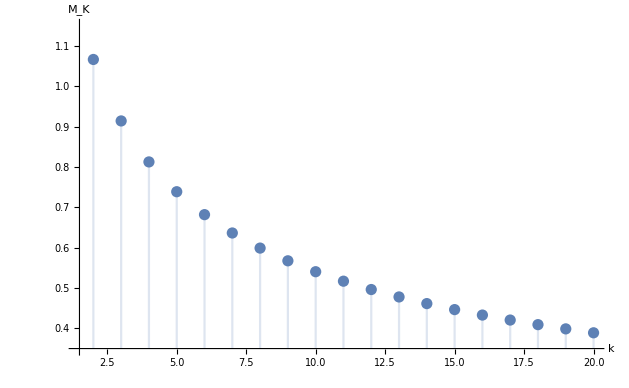

```mathematica
DiscretePlot[Evaluate[M[k]], {k, 2, 20},AxesLabel->{k, Subscript[M, K]},PlotRange->{{1.5,20},{0.35, 1.15}},LabelStyle->Directive[Black,Bold, FontSize->13],Joined->False]
```